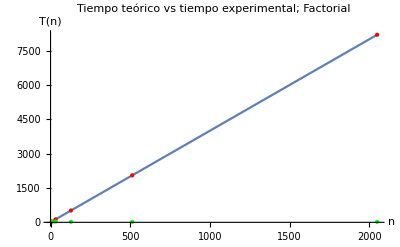

```mathematica
f[n_]:=4*n+3;
funcionFactorial=Plot[f[n],{n,0,2050}];
puntos={{8,f[8]},{32,f[32]},{128,f[128]},{512, f[512]},{2048, f[2048]}};
graficaPuntos=ListPlot[puntos,PlotStyle->{PointSize[Large],Red},AxesLabel->{"Eje X","Eje Y"},PlotRange->All];
puntosNano={{8,20.625464},{32,28.274873},{128,22.260927},{512, 20.289446},{2048, 21.028632}};
graficaPuntosNano=ListPlot[puntosNano,PlotStyle->{PointSize[Large],Green},AxesLabel->{"n","T(n)"},PlotRange->All];
Show[funcionFactorial,graficaPuntos,graficaPuntosNano, PlotRange->All,PlotLabel->"Tiempo teórico vs tiempo experimental; Factorial", 
AxesLabel->{"n","T(n)"}]
```

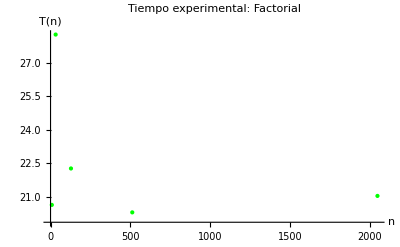

```mathematica
puntos={{8,20.625464},{32,28.274873},{128,22.260927},{512, 20.289446},{2048, 21.028632}};
graficaPuntos=ListPlot[puntos,PlotStyle->{PointSize[Large],Green},AxesLabel->{"n","T(n)"},PlotRange->All,
PlotLabel->"Tiempo experimental: Factorial"]
```

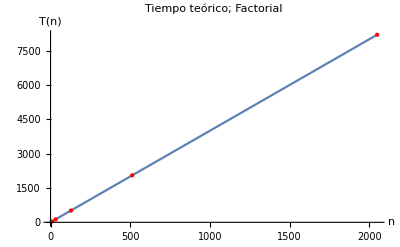

```mathematica
puntos={{8,f[8]},{32,f[32]},{128,f[128]},{512, f[512]},{2048, f[2048]}};
graficaPuntos=ListPlot[puntos,PlotStyle->{PointSize[Large],Red},AxesLabel->{"Eje X","Eje Y"},PlotRange->All];
Show[funcionFactorial,graficaPuntos, PlotRange->All,PlotLabel->"Tiempo teórico; Factorial" ,AxesLabel->{"n","T(n)"}]
```

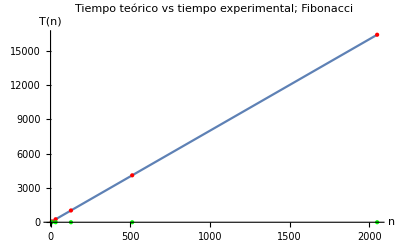

```mathematica
g[n_]:=8*n+5;
funcioFibonacci=Plot[g[n],{n,0,2050}];
puntos={{8,g[8]},{32,g[32]},{128,g[128]},{512, g[512]},{2048, g[2048]}};
graficaPuntos=ListPlot[puntos,PlotStyle->{PointSize[Large],Red},AxesLabel->{"Eje X","Eje Y"},PlotRange->All];
puntosNano={{8,0.001753},{32,0.002598},{128,0.004297},{512,0.012391},{2048,0.04752}};
graficaPuntosNano=ListPlot[puntosNano,PlotStyle->{PointSize[Large],Green},AxesLabel->{"n","T(n)"},PlotRange->All];
Show[funcion,graficaPuntos,graficaPuntosNano, PlotRange->All,PlotLabel->"Tiempo teórico vs tiempo experimental; Fibonacci", 
AxesLabel->{"n","T(n)"}]
```

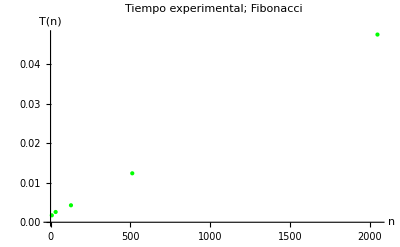

```mathematica
puntosNano={{8,0.001753},{32,0.002598},{128,0.004297},{512,0.012391},{2048,0.04752}};
graficaPuntosNano=ListPlot[puntosNano,PlotStyle->{PointSize[Large],Green},
PlotLabel->"Tiempo experimental; Fibonacci" ,AxesLabel->{"n","T(n)"},PlotRange->All]
```

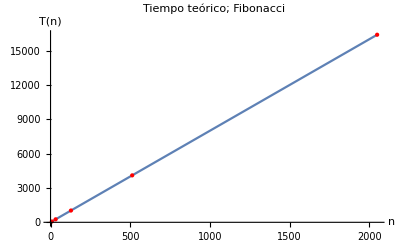

```mathematica
puntosNano={{8,0.001753},{32,0.002598},{128,0.004297},{512,0.012391},{2048,0.04752}};

Show[funcioFibonacci,graficaPuntos, PlotRange->All,PlotLabel->"Tiempo teórico; Fibonacci" ,AxesLabel->{"n","T(n)"}]
```